```mathematica
On[Assert]
$Path=Union[Append[$Path,NotebookDirectory[]]];
<<SmolyakQuadrature`
```

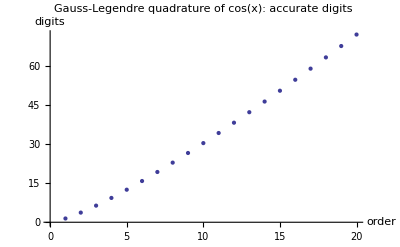

```mathematica
(* Plot the number of accurate digits of Gaussian integration of Cos[x] *)
ListPlot[
With[{prec=100},
Table[-Log[10,N[Abs[gint[Cos,k,prec]-Sin[1]],prec]],{k,20}]]
,PlotLabel->"Gauss-Legendre quadrature of cos(x): accurate digits",AxesLabel->{"order","digits"}]
```

```mathematica
checkAccuracyOrder[gw,10,100,2#-1&];
```

```mathematica
(* Check that KP abscissas are nested *)
Do[Assert[Length[kpAbscissas[n,20]]==Length[Intersection[kpAbscissas[n,20],kpAbscissas[n+1,20]]]],{n,4}]
```

```mathematica
Assert[accuracyOrder[kp,1,20]==1]
Assert[accuracyOrder[kp,2,20]==5]
Assert[accuracyOrder[kp,3,20]==11]
Assert[accuracyOrder[kp,4,20]==23]
Assert[accuracyOrder[kp,5,20]==47]
```

```mathematica
Assert[Min[Table[accuracyOrder[kpDelay[delayFull],n,20]-(2n-1),{n,Length[delayFull]}]]≥0]
```

```mathematica
(* Check that the quadrature formula is the same as gw for legendre polynomial roots *)
Assert[roundPrec[quadrature[( legendreRoots[10]+1)/2,40],20]-roundPrec[gw[10,40],20]==0]
```

```mathematica
(* CC formulas *)
ClearAll[ccAbscissas,ccM,cc]
ccM[1]:=1
ccM[n_]:=2^(n-1)+1
ccAbscissas[1,prec_]:={0}
ccAbscissas[n_,prec_]:=Table[N[-Cos[(Pi (j-1))/(ccM[n]-1)],prec],{j,ccM[n]}]
cc[n_,prec_]:=cc[n,prec]=iteratePrec[quadrature[(ccAbscissas[n,prec]+1)/2,#]&,prec]
```

```mathematica
(* Check that CC abscissas are nested *)
Do[Assert[Length[ccAbscissas[n,20]]==Length[Intersection[ccAbscissas[n,20],ccAbscissas[n+1,20]]]],{n,4}]
(* Check the accuracy order of the CC formulas *)
checkAccuracyOrder[cc,6,30,ccM[#]&];
```

```mathematica
(* check the 4d rule *)
Assert[Length[ecfRule[rule4d9k145]]==145]
Assert[Abs[1-Total[to01cube4d[ecfRule[rule4d9k145]][[All,1]]]]<10^-30]
Assert[Precision[to01cube4d[ecfRule[rule4d9k145]]]>29]
(* check the tetrahedral rule *)
Assert[Length[ecfRule[simplex3d8k43]]==43]
Assert[Abs[6 Total[ecfRule[simplex3d8k43][[All,1]]]-1]<10^-30]
Assert[Max[Abs[Total[ecfRule[simplex3d8k43][[All,2;;]],{2}]-1]]<10^-30]
(* check the triangle rule *)
Assert[Length[ecfRule[simplex2d10k25a]]==25]
Assert[Abs[2 Total[ecfRule[simplex2d10k25a][[All,1]]]-1]<10^-30]
Assert[Max[Abs[Total[ecfRule[simplex2d10k25a][[All,2;;]],{2}]-1]]<10^-30]
```

```mathematica
intTet[1&,{{0,0,0},{1,0,0},{0,1,0},{0,0,1}}];
intTri[1&,{{0,0,0},{1,0,0},{0,1,0}}];
```